# Resource-driven disease dynamics: linking resources, traits, trophic cascades, and instability using loop analysis

State Variables:
S => Susceptible host density
F (I) => Infected host density
Z => Propagule density
A => Algal resource density

Parameters: 
ds => loss rate, hosts
dz => loss rate, propagules
e => conversion efficiency
f => feeding rate, fixed slope or maximum
h => half-saturation constant, feeding rate
k1 => carrying capacity, algal resource
o => propagule yield, fixed slope or maximum
r => growth rate, algal resource
u => per propagule infectivity
v => virulent mortality
theta => reduction of feeding rate, infected hosts

### Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Quiet[<<"/Users/eden/Desktop/RESEARCH/CODE/Dynamica/Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
Quiet[<<"/Users/eden/Downloads/lce.m"]
```

## FIGURE 1 / A3

## Variant 1

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k]
```

```mathematica
Ty3NSP = DynamicalSystem[{
e*((f*A)/(h^2+A^2))*(S+theta*F)*A - ds*S - u*((f*A)/(h^2+A^2))*Z*S,
u*((f*A)/(h^2+A^2))*Z*S - (ds + v)*F,

o*(ds + v)*F - dz*Z - ((f*A)/(h^2+A^2))*(S+theta*F)*Z,
r*A*(1 - A/k)-((f*A)/(h^2+A^2))*A*(S+theta*F)
},
{{S,-1,200},{F,-1,500},{Z,-0.1,10000},{A,-0.01,10}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.14},{dz,0,1},{u,0,2},{v,0,0.2},{o,0,1000000},{theta,0,2},{r,0,2},{k,0.01,6}}]
```

DynamicalSystem[«4 ODEs»,{S,F,Z,A},{e,h,f,ds,dz,u,v,o,theta,r,k}]

```mathematica
Ty3NSPo = Ty3NSP/.{e->8,h -> 0.2314, f->0.0153, dz->0.9, u->1.049, v->0.05157, o->483.8, theta->0.8, r->1}
```

DynamicalSystem[«4 ODEs»,{S,F,Z,A},{ds,k},{dz→0.9,e→8,f→0.0153,h→0.2314,o→483.8,r→1,theta→0.8,u→1.049,v→0.05157}]

Warning: A convergence failure occurred during continuation

Warning: MaxSteps exceeded, terminating branch

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={0,0,0,0,6,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={0,0,0,0.01,0.01,0.000228162568066635}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={0,0,0,0.0210016787592897,0.0210016787592897,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={0.298539468495375,0,0,0.0210016787604464,0.0210390626205936,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={0.109673796892694,35.3258284708665,489.451579950147,0.248118572702429,3.85490140712239,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={0,0,0,6.,6,0.122218214122093}

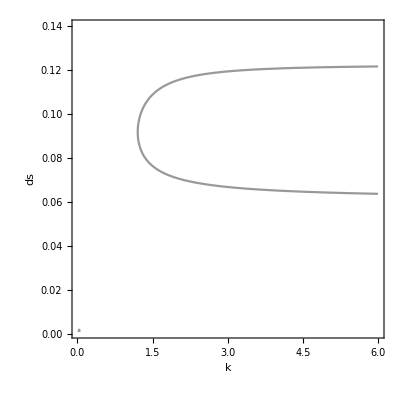

```mathematica
KDSNSP = DisplayParameterChart[Ty3NSPo,{k,ds},MaxStepSize->0.2,MaxSteps->5000(*FrameTicks->{{{0,0.02,0.04,0.06,0.08,0.1},None},{{0,1,2,3,4,5,6},None}}*)]
```

### R0

```mathematica
dSNSP=e*((f*A)/(h^2+A^2))*(S+theta*F)*A - ds*S - u*((f*A)/(h^2+A^2))*Z*S;
dFNSP=u*((f*A)/(h^2+A^2))*Z*S - (ds + v)*F;

dZNSP=o*(ds + v)*F - dz*Z - ((f*A)/(h^2+A^2))*(S+theta*F)*Z;
dANSP=r*A*(1 - A/k)-((f*A)/(h^2+A^2))*A*(S+theta*F);
```

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k]
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
T3EquilibriaNSP=Solve[{dSNSP==0,dFNSP==0,dZNSP==0,dANSP==0},{S,F,Z,A}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{S→0.,F→0.,Z→0.,A→0.},{1},3,{1},{S→(2.65559×10^33 ds k+1.03071×10^35 ds^2 k+39+1-3.48818×10^38 ds^3 (1)^5)/(7.57448×10^32 ds k^2+1.76695×10^34 ds^2 k^2+5.71337×10^34 ds^3 k^2),F→1/1,Z→1/1,A→1}}
 |  |  |  |

```mathematica
T3EquilibriaNSP[[3]]/.{ds->0.035,k->1}
```

{S→28.5694,F→9.24708×10^-16,Z→-1.14624×10^-13,A→0.146434}

Get Boundary S & A to plug into R0

```mathematica
SatBNSP=T3EquilibriaNSP[[3,1,2]];
AatBNSP=T3EquilibriaNSP[[3,4,2]];
```

```mathematica
Clear[ds]
```

R0 Equation

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
R0NSP= (u*((f* AatBNSP)/(h^2+AatBNSP^2))*SatBNSP)/(ds+v)(o*(ds + v))/(dz +((f *AatBNSP)/(h^2+AatBNSP^2))*SatBNSP);
```

```mathematica
FullSimplify[(u*((f*A)/(h^2+A^2))*S)/(ds+v)(o*(ds + v))/(dz +((f *A)/(h^2+A^2))*S)]
```

(8.62761 A S)/(0.053546+1. A^2+0.017 A S)

```mathematica
R0NSP/.{ds->0.06,k->1}
```

234.506

```mathematica
Solve[(R0NSP/.{ds->0.025}) == 1,k]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{k→0.117443}}

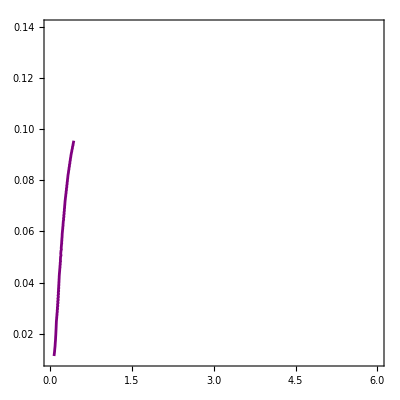

```mathematica
ContourPlot[R0NSP==1,{k,0.01,6},{ds,0.01,0.14},ContourStyle->{Purple,Thickness->0.005,Filling->Right, FillingStyle->Yellow}]
```

```mathematica
S0NSP = (e*((f*k)/(h^2+k^2))*k)/ds
```

(0.1224 k^2)/(ds (0.053546+k^2))

### R0 on cycles - R0 average (Fig. A3)

```mathematica
Clear[k1,k,d,ds, r0, r0current,stest,a];
```

```mathematica
R0CYC[k0_,ds0_]:=
Module[{k1=k0, d = ds0},
(* Equilibrate *)
DisplayTrajectories[Ty3NSP/.{k->k1,ds->d},{{15,0,0,2}},2000, StateVariables->{A,S}, MaxIterations->Infinity,MaxSteps->Infinity];
(* R0 *)
DisplayTrajectories[Ty3NSP/.{k->k1,ds->d},{{Last[First[$Trajectories]][[1]],0,0,Last[First[$Trajectories]][[4]]}},5000, StateVariables->{A,S}, MaxIterations->Infinity,MaxSteps->Infinity,MaxStepSize->0.01];
r0 = 0;
For[a=1,a<=Length[$Trajectories[[1]]],a++,
stest = $Trajectories[[1]][[a]][[1]];
atest = $Trajectories[[1]][[a]][[4]];
r0current = (u*((f* atest)/(h^2+atest^2))*stest)/(d+v) (o*(d + v))/(dz +((f *atest)/(h^2+atest^2))*stest);
r0 = r0 + r0current;
];
r0 = r0/Length[$Trajectories[[1]]];
r0
]
```

```mathematica
R0cyc = {};
granK = 0.04; (* 0.02 *)
granDS = 0.0005; (* 0.0005 *)
startK = 1;
startDS = 0.06;
maxK = 6;
maxDS = 0.13;
For[i=(startK/granK),i<=(maxK/granK),i++,
Clear[k1];
k1 = i * granK;
For[j=(startDS/granDS),j<=(maxDS/granDS),j++,
Clear[d];
d = j * granDS;
AppendTo[R0cyc,{k1, d,R0CYC[k1,d]}];
]
]
```

```mathematica
Export["R0cycle.dat",R0cyc];
```

```mathematica
R0cyc=Import["R0cycle.dat","Table"];
```

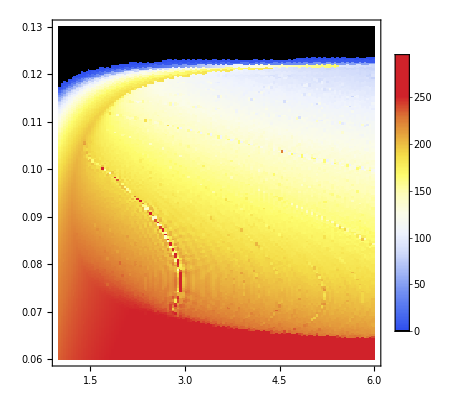

```mathematica
R0cycPlot =ListDensityPlot[Transpose[ArrayReshape[R0cyc[[All,3]],{IntegerPart[(maxK/granK) - (startK/granK)+1],IntegerPart[(maxDS/granDS)-(startDS/granDS)+1]}]],DataRange->{{startK,maxK},{startDS,maxDS}},ColorFunction->(If[#<1,Black,ColorData["TemperatureMap",#/250]]&),ColorFunctionScaling->False,
InterpolationOrder->0, PlotLegends->Automatic]
```

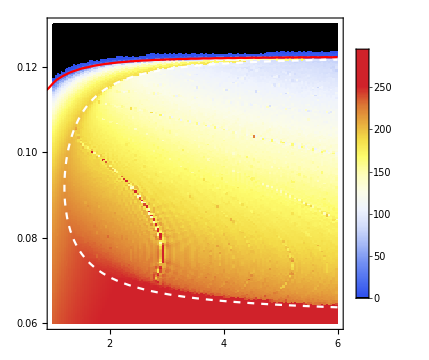

```mathematica
R0PT3= Show[
R0cycPlot ,
RegionPlot[S0NSP>=1 ,{k,0,6},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Opacity[0.0]],
ListLinePlot[KDSNSP[[1]][[1]][[2]][[3]][[1]],PlotStyle->{White,Dashed,Thickness->0.008},PlotRange->All],
LPCNSP2,
ContourPlot[S0NSP==1,{k,0.001,6},{ds,0.00001,0.14},ContourStyle->{Red,Thickness->0.01}],
ImageSize->Medium,
FrameTicks->{{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"}, 0.12},None},{{0,1,2,3,4,5,6},None}},
LabelStyle->{16,Black},
AspectRatio->1,PlotRange->{{startK,maxK},{startDS,maxDS}}, PlotRangeClipping->True,ImageResolution->1000
]
```

### Construct Chart

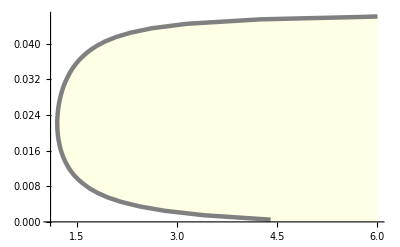

```mathematica
LPCNSP2 = ListLinePlot[{{6,0.04615},{5.78,0.04605},{4.245,0.0455},{3.145,0.0445},{2.62,0.0435},{2.3,0.0425},{2.079,0.0415},{1.915,0.0405},{1.79,0.0395},{1.69,0.0385},{1.609,0.0375},{1.539,0.0365},{1.483,0.0355},{1.434,0.0345},{1.392,0.0335},{1.358,0.0325},{1.326,0.0315},{1.299,0.0305},{1.277,0.0295},{1.258,0.0285},{1.242,0.0275},{1.229,0.0265},{1.218,0.0255},{1.211,0.0245},{1.206,0.0235},{1.203,0.0225},{1.204,0.0215},{1.207,0.0205},{1.213,0.0195},{1.222,0.0185},{1.235,0.0175},{1.25,0.0165},{1.27,0.0155},{1.295,0.0145},{1.325, 0.0135},{1.36,0.0125},{1.403,0.0115},{1.455,0.0105},{1.519,0.0095},{1.598,0.0085},{1.69,0.0075},{1.81,0.0065},{1.96,0.0055},{2.16,0.0045},{2.43,0.0035},{2.81,0.0025},{3.4, 0.0015},{4.4,0.0005}},
PlotStyle->{Gray,Thickness->0.008},PlotRange->All,Filling->Bottom,FillingStyle->Lighter[Yellow,0.9]]
```

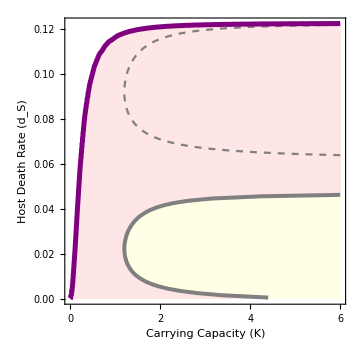

```mathematica
FCNSP = Show[
RegionPlot[S0NSP>=1 ,{k,0,6},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
ListLinePlot[KDSNSP[[1]][[1]][[2]][[3]][[1]],PlotStyle->{Gray,Dashed},PlotRange->All],
LPCNSP2,
ContourPlot[S0NSP==1,{k,0.001,6},{ds,0.00001,0.14},ContourStyle->{Purple,Thickness->0.01}],
ImageSize->Medium,
FrameTicks->{{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"}, 0.12},None},{{0,1,2,3,4,5,6},None}},
FrameLabel->{"Carrying Capacity (K)","Host Death Rate (d_S)"},
LabelStyle->{16,Black},
PlotRange->All, PlotRangeClipping->False
]
```

## Variant 2

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds]
```

```mathematica
Ty32NT3 = DynamicalSystem[{
e*f*(S+theta*F)*A - ds*S - u*f*Z*S,
u*f*Z*S - (ds + v)*F,

(o*f*A)*(ds + v)*F - dz*Z - f*(S+theta*F)*Z,
r*A*(1 - A/k)-f*A*(S+theta*F)
},
{{S,-0.1,200},{F,-0.1,200},{Z,-0.1,200},{A,-0.01,10}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.14},{dz,0,1},{u,0,2},{v,0,0.2},{o,0,1000000},{theta,0,2},{r,0,2},{k,0.01,6}}]
```

DynamicalSystem[«4 ODEs»,{S,F,Z,A},{e,h,f,ds,dz,u,v,o,theta,r,k}]

```mathematica
Ty32NT3o = Ty32NT3/.{e->8,h -> 0.2314, f->0.0153, ds->0.025,dz->0.9, u->1.049, v->0.05157, o->483.8, theta->0.8, r->1,k->3}
```

DynamicalSystem[«4 ODEs»,{S,F,Z,A},{ds→0.025,dz→0.9,e→8,f→0.0153,h→0.2314,k→3,o→483.8,r→1,theta→0.8,u→1.049,v→0.05157}]

```mathematica
KDSNT3 = DisplayParameterChart[Ty32NT3o,{k,ds},MaxStepSize->0.01,MaxSteps->50000]
```

General::munfl: 0.-4.34584737989688×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.+2.20687562260388×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.-4.44659081257122×10^-323 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

### R0

```mathematica
dSNT3=e*f*(S+theta*F)*A - ds*S - u*f*Z*S;
dFNT3=u*f*Z*S - (ds + v)*F;
dZNT3=(o*f*A)(ds + v)*F - dz*Z - f*(S+theta*F)*Z;
dANT3=r*A*(1 - A/k)-f*A*(S+theta*F);
```

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k]
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
T3EquilibriaNT3=Solve[{dSNT3==0,dFNT3==0,dZNT3==0,dANT3==0},{S,F,Z,A}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{S→0.,F→0.,Z→0.,A→0.},5,{S→1/(-3.54589×10^20+2.11193×10^22 ds+8.72388×10^22 ds^2+1.27924×10^21 k-4.27121×10^22 ds k),F→-(1.99249×10^-13 1)/(5157. k^2+20000. ds k^2)-1+1/1,Z→1,A→1/(3.54589×10^24-2.11193×10^26 ds-19 1-22 k+4.27121×10^26 ds k)}}
 |  |  |  |

```mathematica
T3EquilibriaNT3[[3]]/.{ds->0.035,k->1}
```

{S→46.6701,F→0.,Z→0.,A→0.285948}

Get Boundary S & A to plug into R0

```mathematica
SatBNT3=T3EquilibriaNT3[[3,1,2]];
AatBNT3=T3EquilibriaNT3[[3,4,2]];
```

```mathematica
Clear[ds]
```

R0 Equation

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
R0NT3= (u*f*SatBNT3)/(ds+v)((o*f*AatBNT3)*(ds + v))/(dz +f*SatBNT3);
```

```mathematica
R0NT3/.{ds->0.06,k->1}
```

1.37641

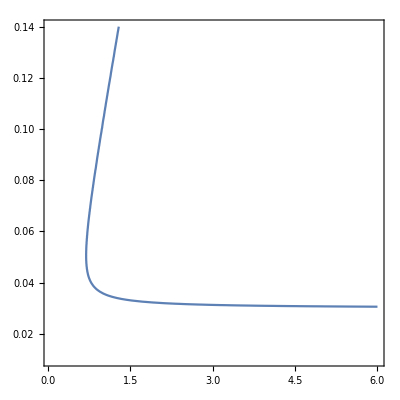

```mathematica
ContourPlot[R0NT3==1,{k,0.05,6},{ds,0.01,0.14}]
```

```mathematica
S0NT3 = (e*f*k)/ds
```

(0.1224 k)/ds

### Construct Chart

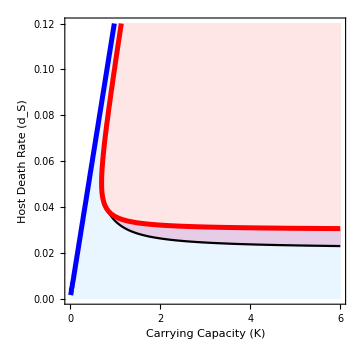

```mathematica
FCNT3 = Show[KDSNT3,
RegionPlot[S0NT3>=1 ,{k,0,6},{ds,0.00,0.12}, BoundaryStyle->None,PlotStyle->Lighter[LightBlue]],
ListLinePlot[KDSNT3[[1]][[1]][[1]][[2]][[1]],PlotStyle->Black,Filling->Top,FillingStyle->Lighter[Purple,0.8]],RegionPlot[R0NT3>=1 ,{k,0,6},{ds,0.00,0.12}, BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
RegionPlot[S0NT3<=1 ,{k,0,6},{ds,0.00,0.12}, BoundaryStyle->None,PlotStyle->White],
ContourPlot[R0NT3==1,{k,0.3,6},{ds,0.02,0.12},ContourStyle->{Red,Thickness->0.01}],
ContourPlot[S0NT3==1,{k,0.01,2},{ds,0.001,0.12},ContourStyle->{Blue,Thickness->0.01}],
ImageSize->Medium,
FrameTicks->{{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"},0.12},None},{{0,1,2,3,4,5,6},None}},
FrameLabel->{"Carrying Capacity (K)","Host Death Rate (d_S)"},
LabelStyle->{16,Black},
PlotRange->All, PlotRangeClipping->False]
```

## Variant 3

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds]
```

```mathematica
Ty3SP = DynamicalSystem[{
e*((f*A)/(h^2+A^2))*(S+theta*F)*A - ds*S - u*((f*A)/(h^2+A^2))*Z*S,
u*((f*A)/(h^2+A^2))*Z*S - (ds + v)*F,

(o*((f*A)/(h^2+A^2))*A)*(ds + v)*F - dz*Z - ((f*A)/(h^2+A^2))*(S+theta*F)*Z,
r*A*(1 - A/k)-((f*A)/(h^2+A^2))*A*(S+theta*F)
},
{{S,-0.1,200},{F,-0.1,200},{Z,-0.1,200},{A,-0.01,10}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.14},{dz,0,1},{u,0,2},{v,0,0.2},{o,0,1000000},{theta,0,2},{r,0,2},{k,0.01,6}}]
```

DynamicalSystem[«4 ODEs»,{S,F,Z,A},{e,h,f,ds,dz,u,v,o,theta,r,k}]

```mathematica
Ty3SPo = Ty3SP/.{e->8,h -> 0.2314, f->0.0153, ds->0.035,dz->0.9, u->1.049, v->0.05157, o->483.8, theta->0.8, r->1,k->1}
```

DynamicalSystem[«4 ODEs»,{S,F,Z,A},{ds→0.035,dz→0.9,e→8,f→0.0153,h→0.2314,k→1,o→483.8,r→1,theta→0.8,u→1.049,v→0.05157}]

Warning: A convergence failure occurred during continuation

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={0,0,0,0.01,0.01,0.000228162568066635}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={0,0,0,0.0210016787592897,0.0210016787592897,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={34.2793594168622,0,0,0.132641510895947,6,0.030271094450697}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={45.4084972909968,0,0,5.19994056621017,6,0.122158090910669}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,A,k,ds}={0,0,0,6.,6,0.122218214122093}

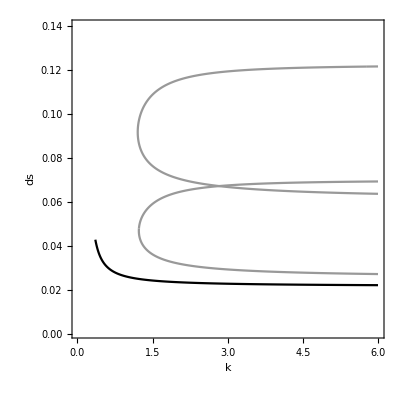

```mathematica
KDSChart = Quiet[DisplayParameterChart[Ty3SPo, {k,ds},MaxStepSize->0.01,MaxSteps->20000]]
```

### R0

```mathematica
dS=e*((f*A)/(h^2+A^2))*(S+theta*F)*A - ds*S - u*((f*A)/(h^2+A^2))*Z*S;
dF=u*((f*A)/(h^2+A^2))*Z*S - (ds + v)*F;

dZ=(o*((f*A)/(h^2+A^2))*A)*(ds + v)*F - dz*Z - ((f*A)/(h^2+A^2))*(S+theta*F)*Z;
dA=r*A*(1 - A/k)-((f*A)/(h^2+A^2))*A*(S+theta*F);
```

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k]
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
T3Equilibria=Solve[{dS==0,dF==0,dZ==0,dA==0},{S,F,Z,A}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{S→0.,F→0.,Z→0.,A→0.},7,{S→(1.06789×10^-27 (4.58724×10^34 ds k+1.06742×10^36 ds^2 k+59+8.49918×10^41 ds^3 Root[1&,5]^7))/(ds (5157.+20000. ds)^2 k^2),F→-1/1,Z→-1,A→Root[126252803874982896959677479 k+489636625460472743686940000 ds k+4+(-184916492840418750000000000000+3399671128125000000000000000000 ds) #1^5&,5]}}
 |  |  |  |

```mathematica
T3Equilibria[[3]]/.{ds->0.035,k->1}
```

{S→28.5694,F→5.04704×10^-15,Z→2.21264×10^-15,A→0.146434}

Get Boundary S & A to plug into R0

```mathematica
SatB=T3Equilibria[[3,1,2]];
AatB=T3Equilibria[[3,4,2]];
```

```mathematica
Clear[ds]
```

R0 Equation

```mathematica
R0= (u*((f* AatB)/(h^2+AatB^2))*SatB)/(ds+v)((o*((f* AatB)/(h^2+AatB^2))*AatB)*(ds + v))/(dz +((f *AatB)/(h^2+AatB^2))*SatB);
```

```mathematica
S0 = (e*((f*k)/(h^2+k^2))*k)/ds
```

(0.1224 k^2)/(ds (0.053546+k^2))

### Drawing Other Bifurcation Curves

Data from from MatCont - see other files

```mathematica
LPC = ListLinePlot[{{1.8909,0.0637},{1.8847,0.0636},{1.8636,0.0635},{1.8529,0.0634},{1.8298,0.0632},{1.7935,0.0629},{1.8268,0.0632},{1.9523,0.0647},{2.1569,0.0665},{2.3060,0.0682},{2.4988,0.0698},{2.6968,0.0713},{2.8980,0.0728},{3.0988,0.0743},{3.2960,0.0757},{3.4890,0.0772},{3.6762,0.0786},{3.8594,0.0801},{4.0349,0.0816},{4.2001,0.0830},{4.3552,0.0845},{4.4968,0.0859},{4.6265,0.0874},{4.7455,0.0888},{4.8519,0.0901},{4.9473,0.0915},{5.0314,0.0928},{5.1090,0.0941},{5.1651,0.0952},{5.2182,0.0964},{5.2621, 0.0976}, {5.2683,0.0978},{5.3033, 0.0990},{5.3275, 0.1},

{5.3448,0.101},{5.3570,0.102},{5.3632,0.103},{5.363,0.104},{5.3557,0.105},
{5.3432,0.106},{5.325,0.107},{5.2994,0.108},{5.2651,0.109},{5.2267,0.11},
{5.1903,0.111},{5.0948,0.1120}


},PlotStyle->{Darker[Darker[Blue]],Thickness->0.005}];
```

```mathematica
LPCi = Fit[{{1.8909,0.0637},{1.8847,0.0636},{1.8636,0.0635},{1.8529,0.0634},{1.8298,0.0632},{1.7935,0.0629},{1.8268,0.0632},{1.9523,0.0647},{2.1569,0.0665},{2.3060,0.0682},{2.4988,0.0698},{2.6968,0.0713},{2.8980,0.0728},{3.0988,0.0743},{3.2960,0.0757},{3.4890,0.0772},{3.6762,0.0786},{3.8594,0.0801},{4.0349,0.0816},{4.2001,0.0830},{4.3552,0.0845},{4.4968,0.0859},{4.6265,0.0874},{4.7455,0.0888},{4.8519,0.0901},{4.9473,0.0915},{5.0314,0.0928},{5.1090,0.0941},{5.1651,0.0952},{5.2182,0.0964},{5.2621, 0.0976}, {5.2683,0.0978},{5.3033, 0.0990},{5.3275, 0.1},
{5.3448,0.101},{5.3570,0.102},{5.3632,0.103},{5.363,0.104},{5.3557,0.105},
{5.3432,0.106},{5.325,0.107},{5.2994,0.108},{5.2651,0.109},{5.2267,0.11},
{5.1903,0.111},{5.0948,0.1120}

},{1,x,x^5},x];
```

```mathematica
LPCiP1 = Plot[LPCi,{x,1.8,6}, PlotStyle->{Thickness->0.006, Darker[Blue], Dashed},Filling->Bottom, FillingStyle->PatternFilling[{"Checkerboard",Lighter[Yellow,0.9],Lighter[Purple,0.8]},ImageScaled[1/50]], PlotRange->{{0,6},{0.06,0.12}}];
```

```mathematica
LPCiP2 = Plot[LPCi,{x,1.8,5.95}, PlotStyle->{Thickness->0.006, Darker[Blue], Dashed}];
```

```mathematica
LPC2 = ListLinePlot[{{2.358,0.0345},{2.7858,0.035},{2.9534,0.0353},{3.1346,0.0357},{3.3190,0.0360},{3.5050,0.0365},{3.6909,0.0369},{3.8754,0.0373},{4.0574,0.0377},{4.2344,0.0381},{4.4034,0.0384},{4.5531,0.0387},{4.6010,0.0387},{6,0.041}},PlotStyle->{Darker[Darker[Blue]],Thickness->0.005}];
```

```mathematica
LPC2i = Fit[{{2.358,0.0345},{2.7858,0.035},{2.9534,0.0353},{3.1346,0.0357},{3.3190,0.0360},{3.5050,0.0365},{3.6909,0.0369},{3.8754,0.0373},{4.0574,0.0377},{4.2344,0.0381},{4.4034,0.0384},{4.5531,0.0387},{4.6010,0.0387},{6,0.041}},{1,x,x^5},x];
```

```mathematica
LPC2iP = Plot[LPC2i,{x,2.39,6},PlotStyle->{Thickness -> 0.006, Darker[Blue], Dashed},Filling->Bottom,FillingStyle->Lighter[Yellow,0.9]];
```

```mathematica
PDo = ListLinePlot[{{3.444,0.0305},{3.044,0.03075},{2.819,0.031},{2.579,0.0315},{2.4305,0.032},{2.379,0.0323},{2.355,0.0325},{2.293,0.033},{2.269,0.0332},{2.228,0.03385},{2.23,0.034},{2.245,0.0341},{2.26,0.0342},{2.3,0.0344},{2.358,0.0345},{2.73,0.0347},{3.042,0.035},{3.64,0.036},{4.14,0.037},{4.64,0.038},{5.31,0.039},{6,0.04}},PlotStyle->{Darker[Darker[Green]],Thickness->0.005}];
```

```mathematica
PD05 = ListLinePlot[{{6,0.02728},{5,0.02766},{4,0.02826},{3.444,0.02879},{3.044,0.02931},{2.819,0.02969},{2.579,0.03081},{2.4305,0.032},{2.379,0.0323},{2.355,0.0325},{2.293,0.033},{2.269,0.0332},{2.23,0.0338},{2.245,0.0339},{2.26,0.034},{2.3,0.0341},{2.358,0.0342}},PlotStyle->{Darker[Blue],Thickness->0.005, Dashed},Filling->Top,FillingStyle->Lighter[Yellow,0.9]];
```

```mathematica
PD1 = Show[ListLinePlot[{{6,0.02728},{5,0.02766},{4,0.02826},{3.444,0.02879},{3.044,0.02931},{2.819,0.02969},{2.579,0.03071}},PlotStyle->{Darker[Blue],Thickness->0.005, Dashed},Filling->Top,FillingStyle->PatternFilling[{"Checkerboard",Lighter[Yellow,0.9],Lighter[Purple,0.8]},ImageScaled[1/50]]],ListLinePlot[{{6,0.03026},{5,0.03034},{4,0.03044},{3.50,0.0305},{2.579,0.03071}},PlotStyle->{Transparent,Thickness->0.005, Dashed},Filling->Top,FillingStyle->Lighter[Yellow,0.9]]];
```

```mathematica
PDi = Fit[Reverse[{{3.444,0.0305},{2.819,0.031},{2.4305,0.032},{2.406,0.0323},{2.369,0.0325},{2.293,0.033},{2.269,0.0332},{2.228,0.03385},{2.23,0.034},{2.358,0.0345},{2.73,0.0347},{3.042,0.035},{3.64,0.036},{4.14,0.037},{4.64,0.038},{5.31,0.039},{6,0.04}}],{1,x,x^4},x];
```

```mathematica
PDiP = Plot[PDi,{x,2.36,6},PlotStyle->{Thickness -> 0.006, Darker[Darker[Green]]}];
```

### Construct Chart

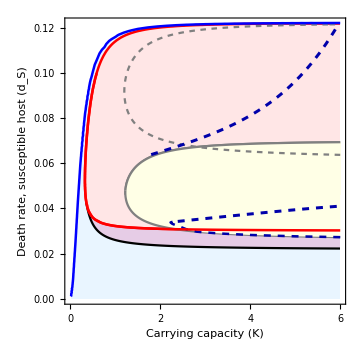

```mathematica
T3SPFC = Show[
RegionPlot[R0<=1 ,{k,0,6},{ds,0,0.12}, BoundaryStyle->None,PlotStyle->Lighter[Purple,0.8]],
RegionPlot[S0>=1 ,{k,0,6},{ds,0,0.13}, BoundaryStyle->None,PlotStyle->Lighter[LightBlue]],
ListLinePlot[KDSChart[[1]][[1]][[1]][[2]][[1]],PlotStyle->Black,Filling->Top,FillingStyle->Lighter[Purple,0.8]],
RegionPlot[R0>=1 && S0>=1,{k,0,6.2},{ds,0,0.122}, BoundaryStyle->{Red,Thickness->0.005},PlotStyle->Lighter[Red,0.9]],
RegionPlot[k>6,{k,0,6.2},{ds,0,0.132},BoundaryStyle->None,PlotStyle->White],
(*LPCiP1,*)
ListLinePlot[KDSChart[[1]][[1]][[3]][[3]][[1]],PlotStyle->Gray,Filling->Bottom,FillingStyle->Lighter[Yellow,0.9]],
RegionPlot[S0<=1 ,{k,0,6},{ds,0,0.12}, BoundaryStyle->None,PlotStyle->White],
ListLinePlot[KDSChart[[1]][[1]][[3]][[3]][[1]],PlotStyle->Gray,PlotRange->All,
Filling->Bottom,FillingStyle->Lighter[Yellow,0.9]],
ListLinePlot[KDSChart[[1]][[1]][[2]][[3]][[1]], PlotRange->All,PlotStyle->{Gray,AbsoluteDashing[4]}],
PD05,
(*PD1,*)
ContourPlot[R0==1,{k,0.3,6},{ds,0.02,0.1},ContourStyle->{Red,Thickness->0.005}],
ContourPlot[S0==1,{k,0.01,6},{ds,0.001,0.13},ContourStyle->{Blue,Thickness->0.005}],
LPCiP2,
LPC2iP,
ImageSize->Medium,
FrameLabel->{"Carrying capacity (K)", "Death rate, susceptible host (d_S)"},
FrameTicks->{{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"},0.12},None},{{0,1,2,3,4,5,6},None}},
LabelStyle->{14,Black},
PlotRange->{{0,6},{0,0.122}}]
```

## FIGURE 2

### A

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k]
```

```mathematica
Ty3SA = DynamicalSystem[{
e*((f*A)/(h^2+A^2))*S*A - ds*S ,
r*A*(1 - A/k)-((f*A)/(h^2+A^2))*A*S
},
{{S,0,200},{A,-0.01,10}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.14},{u,0,2},{r,0,2},{k,0.01,6}}]
```

DynamicalSystem[«2 ODEs»,{S,A},{e,h,f,ds,u,r,k}]

```mathematica
Ty3SAo = Ty3SA/.{e->8,h -> 0.2314, f->0.0153, ds->0.035, u->1.049,r->1,k->1}
```

DynamicalSystem[«2 ODEs»,{S,A},{ds→0.035,e→8,f→0.0153,h→0.2314,k→1,r→1,u→1.049}]

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

«1 more identical outputs»

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,A,k,ds}={0,0.0210016787582075,0.0210016787571253,0.001}

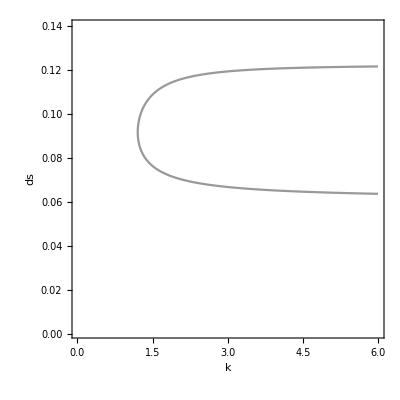

```mathematica
KDSSA = DisplayParameterChart[Ty3SAo,{k,ds},MaxStepSize->0.1,MaxSteps->10000, Tries->10000]
```

#### Sin

Now searching for Sin
First redefine equations

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
dASA = r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*S;
dSSA= e*((f*A)/(h^2+A^2))*S*A - ds*S ;
```

```mathematica
solsSA = Solve[{dASA==0,dSSA==0},{A,S},WorkingPrecision->MachinePrecision];
```

```mathematica
SA = solsSA[[2]]
```

{A→(√ds h)/(√(-ds+e f)),S→(ds e h^2 r+(ds^(3/2) e h k1 r)/(√(-ds+e f))-(√ds e^2 f h k1 r)/(√(-ds+e f)))/(ds^2 k1-ds e f k1)}

Get Boundary S & A to plug into Sin

```mathematica
SatB=SA[[2]];
AatB=SA[[1]];
```

```mathematica
Clear[ds]
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
S0SA= (e*((f*k)/(h^2+k^2))*k)/ds;
```

```mathematica
S0SA/.{ds->0.12075,k->2}
```

1.00027

#### Construct Chart

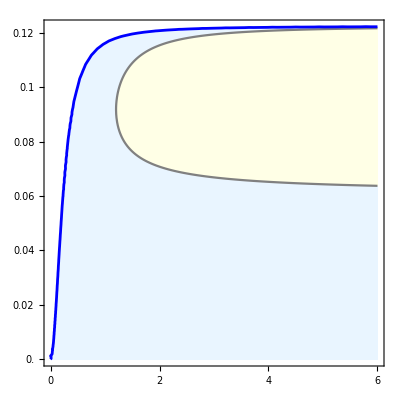

```mathematica
FCSA = Show[KDSSA,
RegionPlot[S0SA>=1 ,{k,0,6},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[LightBlue]],
ListLinePlot[KDSSA[[1]][[1]][[1]][[3]][[1]],PlotStyle->Gray,Filling->Top,FillingStyle->Lighter[Yellow,0.9], PlotRange->All],
ContourPlot[S0SA==1,{k,0,6},{ds,0,0.14},ContourStyle->{Blue,Thickness->0.005}],
(*FrameLabel->{"Carrying Capacity (K)","Host Death Rate (d_S)"},*)
FrameTicks->{{{0.00,0.02,0.04,0.06,0.08,0.10,0.12},None},{{0,1,2,3,4,5,6},None}},FrameLabel->None,LabelStyle->{Black,16}, PlotRange->All]
```

#### Time Series

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
Clear[ds,k1]
ds = 0.09;
Parat3SA=ParametricNDSolveValue[{S'[t]== e*((f*A[t])/(h^2+A[t]^2))*S[t]*A[t] - ds*S[t] ,
A'[t] == r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*S[t],
S[0]==11.17, A[0]==0.325},{S,A},{t,0,6000},{k1}];
```

```mathematica
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@Parat3SA[k1]],{t,0,5500},PlotRange->{{100,300},{0.01,100}},
 PlotStyle->{{Blue,Thick},{Darker[Green],Thick}},
PlotLegends->{"Susceptible","Algae"},TicksStyle->10,AspectRatio->1, LabelStyle->16, Frame->True, FrameLabel->{"Time","Log Concentration"}, FrameStyle->Black]],
{{k1,2},1,8}]
```

### B

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1,Clearance,CR,AstarIII,SstarIII]
```

```mathematica
dAIII = r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*S;
dSIII= e*((f*A)/(h^2+A^2))*S*A - ds*S ;
```

```mathematica
solsIII = Solve[{dAIII==0,dSIII==0},{A,S},WorkingPrecision->MachinePrecision];
```

```mathematica
solsIII[[2]]
```

{A→(√ds h)/(√(-ds+e f)),S→(ds e h^2 r+(ds^(3/2) e h k1 r)/(√(-ds+e f))-(√ds e^2 f h k1 r)/(√(-ds+e f)))/(ds^2 k1-ds e f k1)}

```mathematica
AstarIII:=(√ds h)/(√(-ds+e f))
SstarIII[ds_] := (ds e h^2 r+(ds^(3/2) e h k1 r)/(√(-ds+e f))-(√ds e^2 f h k1 r)/(√(-ds+e f)))/(ds^2 k1-ds e f k1)
```

```mathematica
J11SA = FullSimplify[D[dAIII/A,A]]
```

-r/k1+(f (A-h) (A+h) S)/((A^2+h^2)^2)

```mathematica
CR = ((f*A)/(h^2+A^2));
```

```mathematica
ClearanceI[S_] := (f (A-h) (A+h) S)/((A^2+h^2)^2);
ClearanceII[ds_] := (f (A-h) (A+h) SstarIII[ds])/((A^2+h^2)^2);
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
ds = 0.09;
k1 = 2;
```

```mathematica
P2A = Show[
Plot[CR,{A,0,2}, PlotStyle->Red,AspectRatio->1/2,LabelStyle->16],
Graphics[{Thick,Dashed,InfiniteLine[{{h,0},{h,5}}]}],
PlotRange->All,
Frame->True,FrameTicks->{{{{0.00,"0.00"},0.01,0.02,0.03},None},{{{0.0,"0.0"},0.5,{1.0,"1.0"},1.5,{2.0,"2.0"}},None}}, LabelStyle->{Black,16},ImageSize->Medium
];
```

```mathematica
P2B = Show[
Plot[ClearanceII[0.1],{A,0,2}, PlotStyle->Red,AspectRatio->1/2,LabelStyle->16],
Plot[ClearanceII[0.01],{A,0,2}, PlotStyle->{Dashed,Red},AspectRatio->1/2,LabelStyle->16],
Graphics[{Thick,Dashed,InfiniteLine[{{h,0},{h,5}}]}],
PlotRange->{All, {-0.5,2}},
Frame->True,FrameTicks->{{{{-1.0,"-1.0"},{0.0,"0.0"},{1.0,"1.0"},{2.0,"2.0"}},None},{{{0.0,"0.0"},0.5,{1.0,"1.0"},1.5,{2.0,"2.0"}},None}}, LabelStyle->{Black,16},ImageSize->Medium
];
```

```mathematica
P2A
```

```mathematica
P2B
```

### C

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
dAIII = r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*S;
dSIII= e*((f*A)/(h^2+A^2))*S*A - ds*S ;
```

```mathematica
solsIII = Solve[{dAIII==0,dSIII==0},{A,S},WorkingPrecision->MachinePrecision];
```

```mathematica
solsIII[[2]]
```

{A→(√ds h)/(√(-ds+e f)),S→(ds e h^2 r+(ds^(3/2) e h k1 r)/(√(-ds+e f))-(√ds e^2 f h k1 r)/(√(-ds+e f)))/(ds^2 k1-ds e f k1)}

```mathematica
AstarIII:=(√ds h)/(√(-ds+e f))
SstarIII := (ds e h^2 r+(ds^(3/2) e h k1 r)/(√(-ds+e f))-(√ds e^2 f h k1 r)/(√(-ds+e f)))/(ds^2 k1-ds e f k1)
```

```mathematica
(*Clear[k1];*)
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
ds=0.09;
k1 = 2;
```

```mathematica
P1s = Plot[SstarIII,{k1,0,6}, PlotStyle->Red,AspectRatio->1,LabelStyle->16];
P1slist = P1s[[1]][[1]][[1]][[3]][[1]][[2]][[1]];
P1sfinal = Prepend[P1slist, {0.3856,0}];
```

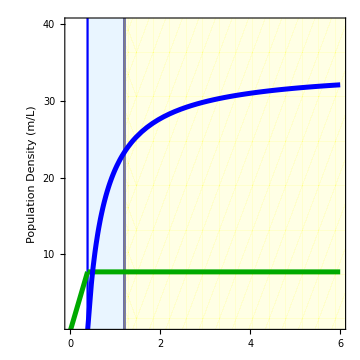

```mathematica
P1 = Show[
RegionPlot[0.3856<x<1.205208,{x,0,7},{y,-10,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[x>1.205208,{x,0,7},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
Plot[k1*20,{k1,0,0.3856}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[AstarIII*20,{k1,0.3856,6}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
ListPlot[P1sfinal,Joined->True ,PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
PlotRange->{{0,6},{1,40}},
Frame->True,FrameLabel->{None,"Population Density (m/L)"},
FrameTicks->{{{0,10,20,30,40},None},{{0,1,2,3,4,5,6},None}},
 LabelStyle->{Black,16},ImageSize->Medium
]
```

### D

```mathematica
Clear[ds]
k1 = 2;
```

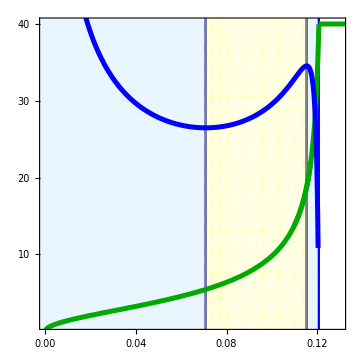

```mathematica
P2 = Show[
RegionPlot[0.07079 > x>-1,{x,-1,0.14},{y,0,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[0.12078 > x>0.115396,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[0.115396 > x>0.07079,{x,0,0.14},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
Plot[k1*20,{ds,0.12078,0.15}, PlotStyle->{Darker[Green], Thickness[0.01]}],
Plot[AstarIII*20,{ds,0,0.15}, PlotStyle->{Darker[Green],Thickness[0.01]}],
Plot[AstarIII*20,{ds,0.11,0.12078}, PlotStyle->{Darker[Green],Thickness[0.01]}],
Plot[SstarIII,{ds,0,0.16}, PlotStyle->{Blue,Thickness[0.01]}],

PlotRange->{{0,0.13},{1,40}},
FrameTicks->{{{0,10,20,30,40},None},{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"},0.12,0.14},None}},
Frame->True, AspectRatio->1,LabelStyle->{Black,16},ImageSize->Medium
]
```

### E

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
dASA = r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*S;
dSSA= e*((f*A)/(h^2+A^2))*S*A - ds*S ;
```

```mathematica
J11SA = FullSimplify[D[dASA,A]];
J12SA = FullSimplify[D[dASA,S]];
J21SA = FullSimplify[D[dSSA,A]];
J22SA = FullSimplify[D[dSSA,S]];
```

```mathematica
JMBase = {{J11SA,J12SA},{J21SA,J22SA}};
JMBase//MatrixForm
```

(r-(2 A r)/k1-(2 A f h^2 S)/((A^2+h^2)^2) | -(A^2 f)/(A^2+h^2)
(2 A e f h^2 S)/((A^2+h^2)^2) | -ds+(A^2 e f)/(A^2+h^2))

```mathematica
FullSimplify[D[dASA/A,A]]
```

-r/k1+(f (A-h) (A+h) S)/((A^2+h^2)^2)

```mathematica
Clear[k1]
ds = 0.09;
SelfLim = -r/k1;
Clearance = (f (AstarIII-h) (AstarIII+h) SstarIII)/((AstarIII^2+h^2)^2);
```

```mathematica
Clear[k1];
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
ds=0.09;
```

```mathematica
SelfLim/.k1->0.3856
Clearance/.k1->0.3856
```

-2.59336

-0.00021096

```mathematica
P3sl = Plot[SelfLim,{k1,0,6}, PlotStyle->Darker[Green],AspectRatio->1,LabelStyle->16];
P3sllist = P3sl[[1]][[1]][[1]][[3]][[1]][[2]][[1]];
P3slfinal = Prepend[P3sllist, {0.3856,-2.59336}];
P3c = Plot[Clearance,{k1,0,6}, PlotStyle->Red,AspectRatio->1,LabelStyle->16];
P3clist = P3c[[1]][[1]][[1]][[3]][[1]][[2]][[1]];
P3cfinal = Prepend[P3clist, {0.3856,0}];
P3com = Plot[SelfLim+Clearance,{k1,0,6}, PlotStyle->Black,AspectRatio->1,LabelStyle->16];
P3comlist = P3com[[1]][[1]][[1]][[3]][[1]][[2]][[1]];
P3comfinal = Prepend[P3comlist, {0.3856,-2.59336}];
```

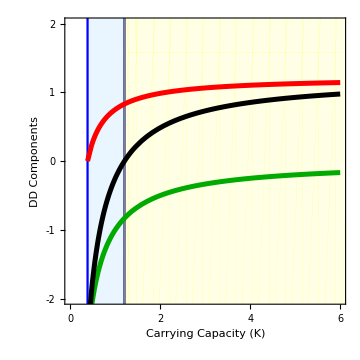

```mathematica
P3 = Show[
RegionPlot[1.205208> x>0.3856,{x,0,7},{y,-10,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[x>1.205208,{x,0,7},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
ListPlot[P3slfinal,Joined->True, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
ListPlot[P3cfinal,Joined->True, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
ListPlot[P3comfinal,Joined->True, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
PlotRange->{{0,6},{-2,2}},AxesOrigin->{0,0},Axes->True,
Frame->True,FrameLabel->{"Carrying Capacity (K)","DD Components"}, 
FrameTicks->{{{-2,-1,0,1,2},None},{{0,1,2,3,4,5,6},None}},LabelStyle->{Black,16},ImageSize->Medium
]
```

### F

```mathematica
Clear[ds]
k1 = 2;
SelfLim = -r/k1;
Clearance = (f (AstarIII-h) (AstarIII+h) SstarIII)/((AstarIII^2+h^2)^2);
```

```mathematica
SstarIII/.{ds->0.1153,k1->2}
```

27.6709

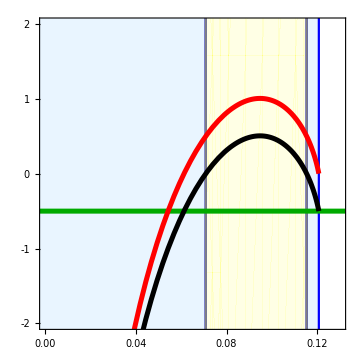

```mathematica
P4 = Show[
RegionPlot[0.07079 > x>-1,{x,-1,0.14},{y,-10,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[0.12078 > x>0.115396,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[0.115396 > x>0.07079,{x,0,0.14},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
Plot[SelfLim,{ds,-1,0.15}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Clearance,{ds,0,0.12078}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[SelfLim + Clearance,{ds,0,0.12078}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,0.13},{-2,2}},AxesOrigin->{0,0},Axes->True,
FrameTicks->{{{-2,-1,0,1,2},None},{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"},0.12,0.14},None}},
Frame->True,FrameLabel->{"Host Death Rate (d_s)"}, LabelStyle->{Black,16},ImageSize->Medium
]
```

## FIGURE 3

### A

```mathematica
FCNSP
```

### B

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
Clear[ds,k1]
ds = 0.035;
Parat3NOSPs=ParametricNDSolveValue[{
S'[t]== e*((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*A[t] - ds*S[t] - u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t],
F'[t]==u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t] - (ds + v)*F[t],
Z'[t]==o*(ds + v)*F[t] - dz*Z[t] - ((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*Z[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]),
S[0]==11.17,F[0]==0,Z[0]==10, A[0]==0.325},{S},{t,0,6000},{k1}];
Parat3NOSPf=ParametricNDSolveValue[{
S'[t]== e*((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*A[t] - ds*S[t] - u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t],
F'[t]==u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t] - (ds + v)*F[t],
Z'[t]==o*(ds + v)*F[t] - dz*Z[t] - ((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*Z[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]),
S[0]==11.17,F[0]==0,Z[0]==10, A[0]==0.325},{F},{t,0,6000},{k1}];
Parat3NOSPz=ParametricNDSolveValue[{
S'[t]== e*((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*A[t] - ds*S[t] - u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t],
F'[t]==u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t] - (ds + v)*F[t],
Z'[t]==o*(ds + v)*F[t] - dz*Z[t] - ((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*Z[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]),
S[0]==11.17,F[0]==0,Z[0]==10, A[0]==0.325},{Z},{t,0,6000},{k1}];
Parat3NOSPa=ParametricNDSolveValue[{
S'[t]== e*((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*A[t] - ds*S[t] - u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t],
F'[t]==u*((f*A[t])/(h^2+A[t]^2))*Z[t]*S[t] - (ds + v)*F[t],
Z'[t]==o*(ds + v)*F[t] - dz*Z[t] - ((f*A[t])/(h^2+A[t]^2))*(S[t]+theta*F[t])*Z[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]),
S[0]==11.17,F[0]==0,Z[0]==10, A[0]==0.325},{A},{t,0,6000},{k1}];
```

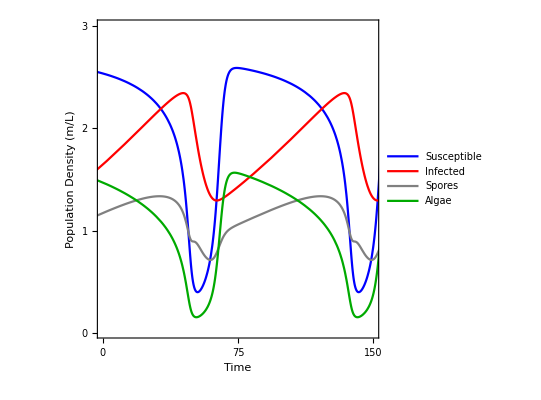

```mathematica
Show[
Plot[Evaluate[#[t]*10& /@Parat3NOSPs[2]],{t,0,500},PlotRange->{{100,250},{0.01,3}}, 
 PlotStyle->{{Blue,Thick}},
PlotLegends->{"Susceptible"},TicksStyle->10, AspectRatio->1, LabelStyle->16,Frame->True, FrameLabel->{"Time","Population Density (m/L)"}, FrameStyle->Black],
Plot[Evaluate[#[t]*0.05& /@Parat3NOSPf[2]],{t,0,500},PlotRange->{{100,250},{0.01,3}}, 
 PlotStyle->{{Red,Thick}},
PlotLegends->{"Infected"},TicksStyle->10, AspectRatio->1, LabelStyle->16,Frame->True, FrameLabel->{"Time","Population Density (m/L)"}, FrameStyle->Black],
Plot[Evaluate[#[t]*0.001& /@Parat3NOSPz[2]],{t,0,500},PlotRange->{{100,250},{0.01,3}}, 
 PlotStyle->{{Gray,Thick}},
PlotLegends->{"Spores"},TicksStyle->10, AspectRatio->1, LabelStyle->16,Frame->True, FrameLabel->{"Time","Population Density (m/L)"}, FrameStyle->Black],
Plot[Evaluate[#[t]& /@Parat3NOSPa[2]],{t,0,500},PlotRange->{{100,250},{0.01,3}}, 
 PlotStyle->{{Darker[Green],Thick}},
PlotLegends->{"Algae"},TicksStyle->10, AspectRatio->1, LabelStyle->16,Frame->True, FrameLabel->{"Time","Population Density (m/L)"}, FrameStyle->Black],
FrameTicks->{{{0,1,2,3},None},{{{100,"0"},{175,"75"},{250,"150"}},None}}
]
```

### C

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
dA=r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*(S+theta*F);
dS=e*((f*A)/(h^2+A^2))*(S+theta*F)*A - ds*S - u*((f*A)/(h^2+A^2))*Z*S;
dF=u*((f*A)/(h^2+A^2))*Z*S - (ds + v)*F;

dZ=o*(ds + v)*F - dz*Z - ((f*A)/(h^2+A^2))*(S+theta*F)*Z;
```

```mathematica
Clear[k1,ds];
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
```

```mathematica
solsSIZA= Solve[{dA==0,dS==0,dF==0, dZ==0},{A,S,F,Z},WorkingPrecision->MachinePrecision];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsSIZA[[7]]/.{ds->0.06,k1->2}
(*solsSIZA[[5]]*)
```

{A→1.9848,S→0.235148,F→0.954834,Z→56.7868}

```mathematica
AstarSIZA=solsSIZA[[5]][[1]][[2]];
SstarSIZA = solsSIZA[[5]][[2]][[2]];
SstarIN = solsSIZA[[3]][[2]][[2]];
FstarSIZA = solsSIZA[[5]][[3]][[2]];
AstarSIZApf=solsSIZA[[7]][[1]][[2]];
SstarSIZApf = solsSIZA[[7]][[2]][[2]];
FstarSIZApf = solsSIZA[[7]][[3]][[2]];
```

```mathematica
Clear[k1];
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
ds=0.03;
```

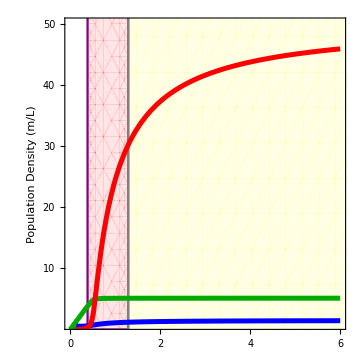

```mathematica
P1SIZA = Show[
RegionPlot[1.2875>x>0.3856,{x,0,7},{y,0,100}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.2875,{x,0,7},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
Plot[k1,{k1,0,0.1318}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[AstarSIZA]*10,{k1,0,0.8}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[AstarSIZA]*10,{k1,0,6}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SstarSIZA]*10,{k1,0.1318,6}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[FstarSIZA],{k1,0.1318,6}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
(*Plot[Re[SstarSIZA]*10+Re[FstarSIZA],{k1,0.1318,6}, PlotStyle->Red,AspectRatio->1,LabelStyle->16],*)

PlotRange->{{0,6},{1,50}},
Frame->True,FrameLabel->{None,"Population Density (m/L)"},
FrameTicks->{{{0,10,20,30,40,50},None},{{0,1,2,3,4,5,6},None}},
 LabelStyle->{Black,16},ImageSize->Medium
]
```

### D

```mathematica
Clear[ds]
k1 = 2;
```

Note that there are multiple segments here at different equilibria as the indexing of equilibria from Mathematica’s ‘Solve’ can change across parameter space.

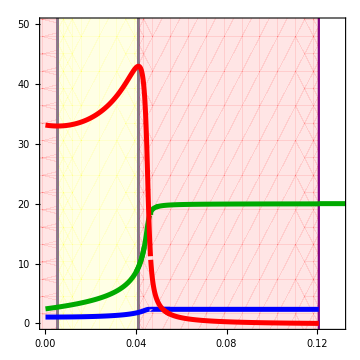

```mathematica
P2SIZA = Show[
RegionPlot[0.005329> x>-1,{x,-1,0.15},{y,-10,100}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.12078> x>0.041056,{x,0,0.15},{y,-10,100}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.041056> x>0.005329,{x,0,0.15},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
Plot[k1*10,{ds,0.12078,0.15}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[AstarSIZA]*10,{ds,0,0.046}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SstarSIZA]*10,{ds,0,0.046}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[FstarSIZA],{ds,0,0.046}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
(*Plot[Re[SstarSIZA]*10+Re[FstarSIZA],{ds,0,0.0464}, PlotStyle->Red,AspectRatio->1,LabelStyle->16],*)

(*Plot[Re[SstarSIZA]*10+Re[FstarSIZA],{ds,0.04,0.04645}, PlotStyle->Red,AspectRatio->1,LabelStyle->16],*)
Plot[Re[SstarSIZApf]*10,{ds,0.0464,0.055}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[AstarSIZApf]*10,{ds,0.04,0.12078}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SstarSIZApf]*10,{ds,0.04,0.12078}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[FstarSIZApf],{ds,0.047,0.12078}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
(*Plot[Re[SstarSIZApf]*10+Re[FstarSIZApf],{ds,0.047,0.12078}, PlotStyle->Red,AspectRatio->1,LabelStyle->16],*)

Plot[Re[AstarSIZA]*10,{ds,0.04,0.046}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[FstarSIZA],{ds,0.047,0.05}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[AstarSIZApf]*10,{ds,0.0464,0.05}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[FstarSIZApf],{ds,0.0465,0.055}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
(*Plot[Re[SstarSIZApf]*10+Re[FstarSIZApf],{ds,0.0465,0.055}, PlotStyle->Red,AspectRatio->1,LabelStyle->16],*)
Plot[Re[FstarSIZA],{ds,0.0453,0.0464}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
PlotRange->{{0,0.13},{0,50}},
Frame->True,
FrameTicks->{{{0,10,20,30,40,50},None},{{{0.00,"0.00"},0.02,0.04, 0.06,0.08,{0.10,"0.10"},0.12},None}},
 LabelStyle->{Black,16},ImageSize->Medium
]
```

### E

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
J11T3
```

r-(2 A r)/k1-(2 A f h^2 (S+F theta))/((A^2+h^2)^2)

```mathematica
FullSimplify[D[r*A*(1 - A/k1)/A,A]]
```

-r/k1

```mathematica
FullSimplify[D[-((f*A)/(h^2+A^2))*A*(S+theta*F)/A,A]]
```

(f (A-h) (A+h) (S+F theta))/((A^2+h^2)^2)

```mathematica
Clear[k1]
ds = 0.03;
SelfLimSIZA = -r/k1;
ClearanceSIZA = (f (AstarSIZA-h) (AstarSIZA+h) (SstarSIZA+FstarSIZA theta))/((AstarSIZA^2+h^2)^2);
SelfLimSIZApf = -r/k1;
ClearanceSIZApf = (f (AstarSIZApf-h) (AstarSIZApf+h) (SstarSIZApf+FstarSIZApf theta))/((AstarSIZApf^2+h^2)^2);
```

```mathematica
(*Clear[k1];*)
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
ds=0.03;
k1 = 2;
```

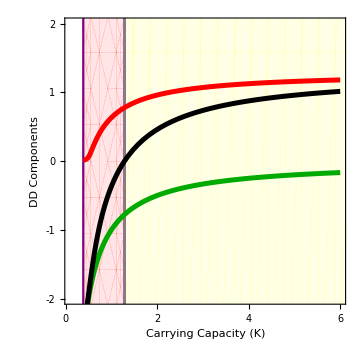

```mathematica
P3SIZA = Show[
RegionPlot[1.2875>x>0.3856,{x,0,7},{y,-10,10}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>1.2875,{x,0,7},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
Plot[Re[SelfLimSIZA],{k1,0,6}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[ClearanceSIZA],{k1,0.3856,6}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimSIZA]+Re[ClearanceSIZA],{k1,0,6}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0.1,6},{-2,2}},
Frame->True,
FrameTicks->{{{-2,-1,0,1,2},None},{{0,1,2,3,4,5,6},None}},FrameLabel->{"Carrying Capacity (K)","DD Components"}, LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

### F

```mathematica
Clear[ds]
k1 = 2;
SelfLimSIZA = -r/k1;
ClearanceSIZA = (f (AstarSIZA-h) (AstarSIZA+h) (SstarSIZA+FstarSIZA theta))/((AstarSIZA^2+h^2)^2);
SelfLimSIZApf = -r/k1;
ClearanceSIZApf = (f (AstarSIZApf-h) (AstarSIZApf+h) (SstarSIZApf+FstarSIZApf theta))/((AstarSIZApf^2+h^2)^2);
```

Note that there are multiple segments here at different equilibria as the indexing of equilibria from Mathematica’s ‘Solve’ can change across parameter space.

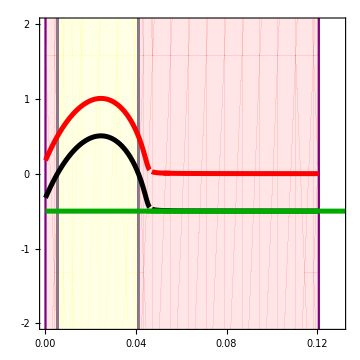

```mathematica
P4SIZA = Show[
RegionPlot[0.005329> x>0,{x,0,0.15},{y,-10,100}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.12078> x>0.041056,{x,0,0.15},{y,-10,100}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.041056> x>0.005329,{x,0,0.15},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[ClearanceSIZA],{ds,0,0.046}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimSIZA] + Re[ClearanceSIZA],{ds,0,0.046}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],


Plot[Re[ClearanceSIZApf],{ds,0.047,0.055}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimSIZApf] + Re[ClearanceSIZApf],{ds,0.047,0.055}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],


Plot[Re[ClearanceSIZApf],{ds,0.047,0.12078}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimSIZApf] + Re[ClearanceSIZApf],{ds,0.0464,0.12078}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[SelfLimSIZA],{ds,0,0.046}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimSIZApf],{ds,0.045,0.12078}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[SelfLimSIZApf],{ds,0.0464,0.14}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,0.13},{-2,2}},
Frame->True,
FrameTicks->{{{-2,-1,0,1,2},None},{{{0.00,"0.00"},0.02,0.04, 0.06,0.08,{0.10,"0.10"},0.12},None}},FrameLabel->{"Host Death Rate (d_s)"}, LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```